## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData},
gridLabel={"k","(X^k)","f(X^k)","Sum[α_i*e_i]"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
For[i=1,i≤Length[points],i++,gridData[[i,4]]="( "<>ToString[SetAccuracy[norms[[i,1]],4]]<>", "<>ToString[SetAccuracy[norms[[i,2]],4]]<>" )"
];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,setX_,setY_,{points_,fValues_}]:=Module[{},
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
Antigrad[point_, func_] := -Grad[func[{x, y}], {x, y}] /. {x->point[[1]],y->point[[2]]};
```

## Алгоритм

```mathematica
Algorithm[{x0_, y0_},func_,ϵ1_,ϵ2_,Method_] := Module [
{
X = {{x0,y0}+{1,1},{x0, y0}},
y = {func[{x0, y0}]+1,func[{x0, y0}]},
mincoefs={},
direct={},
temp={},
basisvectors=IdentityMatrix[2],
i,S=0
},
If[Method ==2,AppendTo[basisvectors,2*{1,1}];];
While[(Norm[X⟦-1⟧-X⟦-2⟧] ≥ ϵ1)||(Abs[y⟦-1⟧-y⟦-2⟧]≥ϵ2),
Print[basisvectors];
For[i=1,i<=Length@basisvectors,++i,
S= Sum[mincoefs⟦j⟧*basisvectors⟦j⟧,{j,1,Length@mincoefs}];
AppendTo[mincoefs,NArgMin[func[Last@X + α * basisvectors⟦i⟧+S], α]];
];
temp=Sum[mincoefs⟦i⟧*basisvectors⟦i⟧,{i,1,Length@mincoefs}] ;
AppendTo[X, Last@X+temp ];
AppendTo[y, func[Last@X]];
If[Method ==3,
basisvectors⟦1⟧=temp;
If[temp.{1,0}==0,
basisvectors⟦2⟧={1,0},
basisvectors⟦2⟧={0,1};
];
basisvectors⟦2⟧=basisvectors⟦2⟧-(basisvectors⟦2⟧.basisvectors⟦1⟧)/(basisvectors⟦1⟧.basisvectors⟦1⟧)*basisvectors⟦1⟧;
];
Print[Method==4&&Abs[mincoefs⟦1⟧]>0 &&Abs[mincoefs⟦2⟧]>0];
If[Method==4&&Abs[mincoefs⟦1⟧]>0 &&Abs[mincoefs⟦2⟧]>0,
basisvectors={basisvectors⟦2⟧,temp};
];
AppendTo[direct,temp];
Print[mincoefs];
mincoefs={};
] ;
AppendTo[direct,temp];
{X[[2;;]], y[[2;;]],direct}
];
```

## Функции:

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
g[{x_,y_}]:=8 x^2+5 y^2-4x y + 8 √5(x+2y)+64;
rosenbrok[{x_,y_}]:=(1-x)^2+10(y-x^2)^2;
```

## Вычисления:

```mathematica
(*Normal 1
Hooke—Jeeves 2
Rosenbrok 3
Paull 4*)
ϵ1=10^-3;
ϵ2=10^-3;
```

### Первый пример:

```mathematica
func =g;(*x0 = {√5,0}, x1 = {0 , 2 √5}*)
Res = Algorithm[{0,2 √5}, func, ϵ1,ϵ2,4];
X = Res[[1]];
Y = Res[[2]];
setX = {x,-7,7};
setY ={y,-7,7};
```

### Второй пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
Res = Algorithm[{-1,-2}, func, ϵ1,ϵ2,4];
X = Res[[1]];
Y = Res[[2]];
setX = {x,-7,7};
setY ={y,-7,7};
```

{{1,0},{0,1}}

True

{1.00249,2.00001}

{{0,1},{1.00249,2.00001}}

True

{2.19512×10^-16,0.00251572}

{{1.00249,2.00001},{0.00252199,0.00503145}}

True

{4.30539×10^-18,-4.4989×10^-14}

## Результаты:

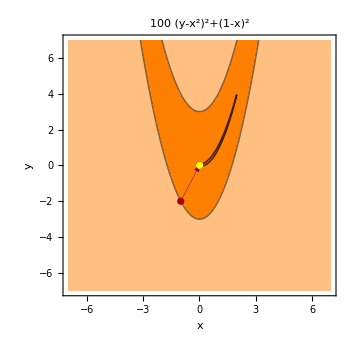

k | (X^k) | f(X^k) | Sum[α_i*e_i]
0 | ( -1.000, -2.000 ) | 904. | ( 1.002, 2.000 )
1 | ( 0.002, 0. ) | 0.995 | ( 0.003, 0.005 )
2 | ( 0.005, 0.005 ) | 0.993 | ( 0., 0. )
3 | ( 0.005, 0.005 ) | 0.993 | ( 0., 0. )

```mathematica
PlotMethod[func,setX,setY,{X, Y}]
MakeTable[Res]
```